```mathematica
MapThread[#1[#2]&,{{f, g}, {1, 2}}]
```

{f[1],g[2]}

```mathematica
fullfunc[mufuncspec_]:= 
If[AssociationQ[mufuncspec], 
AssociationThread[Keys[mufuncspec]->MapThread[#1[#2]&,{Values[mufuncspec], Values[#]}]]&, MapAt[mufuncspec, #, Key["Rule"]]&]
```

```mathematica
fullfitfunc[evospec_, "Lifetime"]:= Module[
{ruleQ = KeyExistsQ[evospec["MutationFunction"], "Rule"], 
initQ = KeyExistsQ[evospec["MutationFunction"], "InitialConditions"]},
cafunc = CellularAutomaton[#1, #2, evospec["StepSpec"]]&

Which[
ruleQ && initQ,
If[#==0,-Infinity(*-infinity*),evospec["StepSpec"]-#+1]&[
LengthWhile[Reverse[CellularAutomaton[#1, #2, evospec["StepSpec"]]],Total[#]==0&]
]&,
ruleQ,
If[#==0,-Infinity(*-infinity*),evospec["StepSpec"]-#+1]&[
LengthWhile[Reverse[CellularAutomaton[#1,evospec["StartingInitialConditions"],evospec["StepSpec"]]],Total[#]==0&]
]&,
True,
If[#==0,-Infinity(*-infinity*),evospec["StepSpec"]-#+1]&[
LengthWhile[Reverse[CellularAutomaton[evospec["StartingRule"], #2, evospec["StepSpec"]]],Total[#]==0&]
]&
]]
```

```mathematica
fullmufunc[fullmuspec_]:= 
If[AssociationQ[fullmuspec], 
Association[KeyValueMap[#1->Lookup[fullmuspec, #1,(#&)][#2]&,#]]&,
If[ListQ[fullmuspec],
MapThread[#1[#2]&, {fullmuspec, #}]&],
fullmuspec]
```

```mathematica
getcafunc[evospec_]:= Module[
{ruleQ = KeyExistsQ[evospec["MutationFunction"], "Rule"], 
initQ = KeyExistsQ[evospec["MutationFunction"], "InitialConditions"]},
Which[ruleQ && initQ,##&, ruleQ, Sequence@@{#1, evospec["StartingInitialConditions"]}&, True, Sequence@@{evospec["StartingInitialConditions"], #2}&]]
```

```mathematica
extrapropkeys = If[evospec["IncludeKeys"], Position[initialkeys, {"MutatedRule","MutatedFitness"}];
```

```mathematica
Join[#, fitnessfunction[Join[#, merged["MutationFunction"][#]]]]
```

```mathematica
getmufunc[args_]:= 
If[ListQ[args], If[Length[args]>1, 
RandomRuleMutation[#Rule, ]], ]
```

```mathematica
"MutationFunction"->1
```

```mathematica
"MutationFunction"->{1, "Symmetric"->False, "Quiescent"->True}
```

```mathematica
"MutationFunction"->"Rule"->{1, "Symmetric"->False, "Quiescent"->True}
```

```mathematica
"MutationFunction"->"InitialCondition"-> 1
```

```mathematica
"MutationFunction"->"InitialCondition"-> 2
```

```mathematica
"MutationFunction"->{"Rule"-> 1, "InitialCondition"-> 2}
```

```mathematica
"MutationFunction"-><|"Rule"-> 1, "InitialCondition"-> 2|>
```

```mathematica
"MutationFunction"-><|"Rule"->(RandomRuleMutation[#Rule]&)|>
```

```mathematica
"Mutat"
```

```mathematica
?(_String ||List[_String..])
```

```mathematica
AdaptiveCellularAutomaton[evospec_][sequencespec_]:=AdaptiveCellularAutomaton[evospec,sequencespec]
```

Part::pkspec1: The expression evospec_ cannot be used as a part specification.

Function::slot1: (RandomRuleMutation[#Rule]&)[<|Rule→{31381059609,3,1},InitialCondition→{{1},0},MutatedRule→{31381059609,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>⟦evospec_⟧] is expected to have an Association as the first argument.

Join::incpt: Incompatible elements in Join[<|Rule→{31381059609,3,1},InitialCondition→{{1},0},MutatedRule→{31381059609,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>⟦evospec_⟧,<|MutatedRule→RandomRuleMutation[#Rule]|>] cannot be joined.

Function::slot1: (CellularAutomaton[If[KeyExistsQ[<|StartingRule→{0,3,1},StartingInitialCondition→{{1},0},StepSpec→100,Iterations→100,MutationFunction→<|MutatedRule→(RandomRuleMutation[#Rule]&)|>,FitnessFunction→Lifetime,SelectionFunction→(#MutatedFitness≥#Fitness&)|>,MutationRule],#Rule,<|«1»|>[StartingRule]],«1»,«1»]&)[«1»] is expected to have an Association as the first argument.

General::stop: Further output of Function::slot1 will be suppressed during this calculation.

Set::write: Tag Join in Join[<|Rule→{31381059609,3,1},InitialCondition→{{1},0},MutatedRule→{31381059609,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>⟦evospec_⟧,<|MutatedRule→RandomRuleMutation[#Rule]|>][MutatedFitness] is Protected.

Join::incpt: Incompatible elements in Join[If[#MutatedFitness≥#Fitness,newstate[Rule]=newstate[MutatedRule];newstate[Fitness]=newstate[MutatedFitness];newstate⟦evospec_⟧,newstate⟦evospec_⟧],<|MutatedRule→RandomRuleMutation[#Rule]|>] cannot be joined.

General::stop: Further output of Join::incpt will be suppressed during this calculation.

Set::write: Tag Join in Join[If[#MutatedFitness≥#Fitness,newstate[Rule]=newstate[MutatedRule];newstate[Fitness]=newstate[MutatedFitness];newstate⟦evospec_⟧,newstate⟦evospec_⟧],<|MutatedRule→RandomRuleMutation[#Rule]|>][MutatedFitness] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

SetDelayed::write: Tag List in {evospec_[<|Rule→{0,3,1},InitialCondition→{{1},0},MutatedRule→None,MutatedInitialCondition→None,MutatedFitness→None,Fitness→1|>],evospec_[<|Rule→{31381059609,3,1},InitialCondition→{{1},0},MutatedRule→{31381059609,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>⟦evospec_⟧],«48»,«51»}[«13»] is Protected.

$Failed

```mathematica
AdaptiveCellularAutomaton[evospec_Association][sequencespec_, propertyspec_]:=AdaptiveCellularAutomaton[evospec,sequencespec, propertyspec]
```

Part::pkspec1: The expression evospec_Association cannot be used as a part specification.

Function::slot1: (RandomRuleMutation[#Rule]&)[<|Rule→{2187,3,1},InitialCondition→{{1},0},MutatedRule→{2187,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>⟦evospec_Association⟧] is expected to have an Association as the first argument.

Join::incpt: Incompatible elements in Join[<|Rule→{2187,3,1},InitialCondition→{{1},0},MutatedRule→{2187,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>⟦evospec_Association⟧,<|MutatedRule→RandomRuleMutation[#Rule]|>] cannot be joined.

Function::slot1: (CellularAutomaton[If[KeyExistsQ[<|StartingRule→{0,3,1},StartingInitialCondition→{{1},0},StepSpec→100,Iterations→100,MutationFunction→<|MutatedRule→(RandomRuleMutation[#Rule]&)|>,FitnessFunction→Lifetime,SelectionFunction→(#MutatedFitness≥#Fitness&)|>,MutationRule],#Rule,<|«1»|>[StartingRule]],«1»,«1»]&)[«1»] is expected to have an Association as the first argument.

General::stop: Further output of Function::slot1 will be suppressed during this calculation.

Set::write: Tag Join in Join[<|Rule→{2187,3,1},InitialCondition→{{1},0},MutatedRule→{2187,3,1},MutatedInitialCondition→None,MutatedFitness→1,Fitness→1|>⟦evospec_Association⟧,<|MutatedRule→RandomRuleMutation[#Rule]|>][MutatedFitness] is Protected.

Join::incpt: Incompatible elements in Join[If[#MutatedFitness≥#Fitness,newstate[Rule]=newstate[MutatedRule];newstate[Fitness]=newstate[MutatedFitness];newstate⟦evospec_Association⟧,newstate⟦evospec_Association⟧],<|MutatedRule→RandomRuleMutation[#Rule]|>] cannot be joined.

General::stop: Further output of Join::incpt will be suppressed during this calculation.

Set::write: Tag Join in Join[If[#MutatedFitness≥#Fitness,newstate[Rule]=newstate[MutatedRule];newstate[Fitness]=newstate[MutatedFitness];newstate⟦evospec_Association⟧,newstate⟦evospec_Association⟧],<|MutatedRule→RandomRuleMutation[#Rule]|>][MutatedFitness] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

SetDelayed::write: Tag List in {evospec_Association[<|Rule→{0,3,1},InitialCondition→{{1},0},MutatedRule→None,MutatedInitialCondition→None,MutatedFitness→None,Fitness→1|>],«49»,«51»}[sequencespec_,propertyspec_] is Protected.

$Failed

```mathematica
OperatorApplied[AdaptiveCellularAutomaton, 2]
```

OperatorApplied[AdaptiveCellularAutomaton,2]

```mathematica
ClearAll[fullmutationform];
fullmutationform[mufuncspec_]:= If[!MatchQ[mufuncspec, _Rule] && !MatchQ[mufuncspec, List[_Rule..]]&&!AssociationQ[mufuncspec], 
<|"MutatedRule"-> getmutationfunction[mufuncspec, "Rule"][#]|>&,
Association[KeyValueMap[StringJoin["Mutated", #1]-> getmutationfunction[#2, #1][#],Association[mufuncspec]]]&
]
```

```mathematica
Table[AdaptiveCellularAutomaton[<|"Rule"-> {0, 2, 2},"Depth"->500, "Cut"->200|>, "Final", "Fitness"], 10]
```

{1,1,1,1,1,1,1,1,1,1}

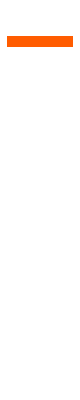

```mathematica
AdaptiveCellularAutomaton[<|"Rule"-> {0, 2, 2},"Depth"->1000|>, "Breakthroughs", "Plot"->30]
```

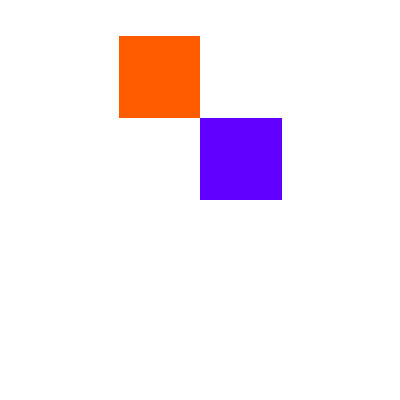
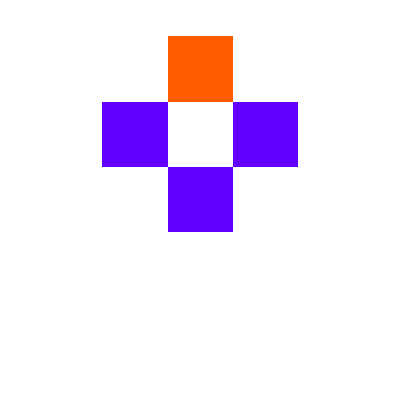
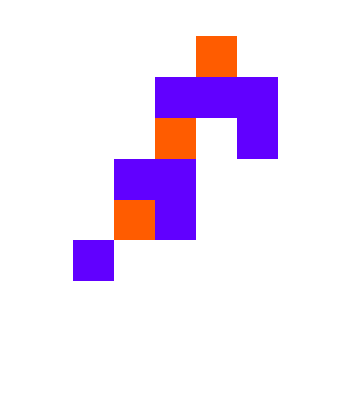
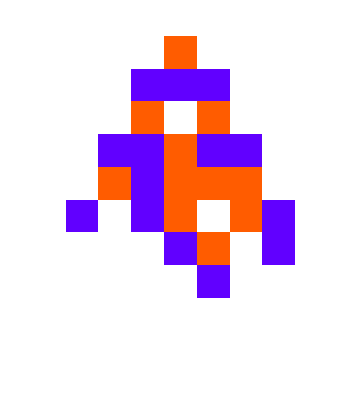
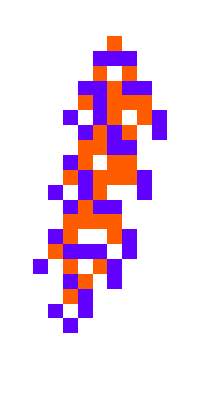
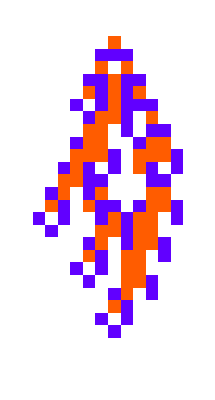
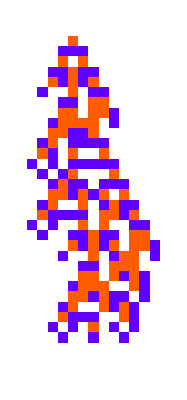
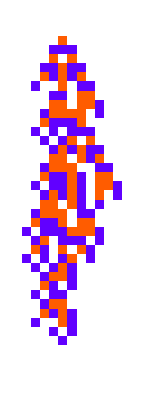
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AdaptiveCellularAutomaton[<|"Depth"->500|>, "Breakthroughs", (ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#Rule, #InitialCondition, #Fitness + 1], ColorRules->colorrules, ImageSize->10Sqrt[#Fitness]]&)]
```

```mathematica
Grid[{GraphicsRow[#]}&/@Values[Module[
{deep=2000,cut=100,ru,life,evo,data,init={1}},
ParallelTable[SeedRandom[426777+i];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#],"Symmetric"->True],
life={{"[◼]", "TestLifetime"}}[ru,init,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,2,2},1},deep];
evo=First/@SplitBy[evo,Last];
i->Map[CompoundExpression[
data=CellularAutomaton[
First[#],{init,0},Last[#]+2],
data=ArrayPad[#,2]&/@data,
ArrayPlot[data,
ImageSize->{Automatic,15Sqrt[Length[data]+1]},
Mesh->True,MeshStyle->Opacity[.1]
]
]&,
evo],{i,{1,5,29,30,54}}]]
],Alignment->Left,Frame->False,
Dividers->{False,{False,{True},False}},FrameStyle->LightGray]
```